## Developing tools for maximization

General instructions: 

1. To evaluate Mathematica code, get the cursor in the cell containing the code and his Shift+Enter.

2. Each occurrence of  ## corresponds to a problem. The problems are rewritten at the end of the notebook in a section entitled: Problems.  That section should be copied into a new Mathematica notebook. Your answers will be put in the new notebook.

3. Do not write Mathematica code and text in the same cell. In the cells where you are writing text, you need to format the cell for text. You can use the Format/Style/Text from the bar above, or Alt+7 to format it for text. You don’t need to format it for code.

4. This will be due on Friday, March 11. Please put a .pdf copy of your solutions on Canvas.

## Analytical tools

We begin by developing an understanding of the Mathematica commands that will help us solve equations. We will look at two commands: Solve and NSolve. Let’s start with a simple example. Get the cursor into the cell below and hit Shift+Enter. This will evaluate the code.

```mathematica
Solve[2x==7]
```

Let’s take a look at that little bit of code and the output that Mathematica gave us. Here are some things to notice:

1. Mathematica distinguishes between lower case and capital letters. Commands which are built into Mathematica always begin with capitals. So, when I make my own commands, I always define it with a lower case letter so as not to have it confused with something Mathematica already knows.

2. Solve solves equations. That’s probably why they named it that.

3. Mathematica is telling us that the answer is 7/2 a little bit differently than we are used to, by using an arrow instead of an =.

4. To  describe the equation I wanted solved, I need to use two equal signs in it. One equal sign is used to define things; two equal signs are used as the relation of equivalence. 

## In new cells, experiment with this by typing and evaluating the following:

        A. Solve[2x=7]
        B. a=9; Solve[2x==a] (that’s a semicolon in there)
        C. a=9 [Return] Solve[2x==a] (the carriage return is not Shift+Return).
        
Sum up what you have deduced about semi-colons, the Solve command, and use of equal signs. In particular, what’s going on in the second bit of code?

## In new cells, experiment with this by typing and evaluating the following:

      C. Solve [3x==y]
      D. Solve[3x==y,{x}].

Sum up what you have deduced about the Solve command and solving for particular variables.

We now introduce a related command, NSolve. Again, evaluate the following code:

```mathematica
NSolve[2x==7]
```

One easy distinction that we can make between the two commands is to say that NSolve solves things in decimals. To verify this, evaluate the two following commands:

```mathematica
Solve[x^2==5]
```

```mathematica
NSolve[x^2==5]
```

To really appreciate the difference between these two commands, let’s try it on a more complicated problem: finding out where a parabola meets a circle. The commands will be:

NSolve[y==3 x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]

and 

Solve[y==3 x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]

Before we evaluate these, here’s a quick comment on the code:We want Mathematica to solve two equations in two unknowns. To feed it two equations, we use two ampersands “&&”. Alternatively, we could have written NSolve[And[y==3 x^2+1,(x-1)^2+(y-7)^2==10],{x,y}]. 

Most people find the “&&” less confusing.

Now put each of these commands in its own cell (you can cut-and-paste) and evaluate the code and see what you think. Here are the commands again.

NSolve[y==3 x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]

and 

Solve[y==3 x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]

## What are the pros and cons of using NSolve instead of Solve?

## Graphical tools

We are going to rely heavily on the Mathematica command: ContourPlot. We will be using this command in two different ways. The first is to draw a curve in the plane that is the graph of some equation. Let’s start with an example that we will thoroughly dissect:

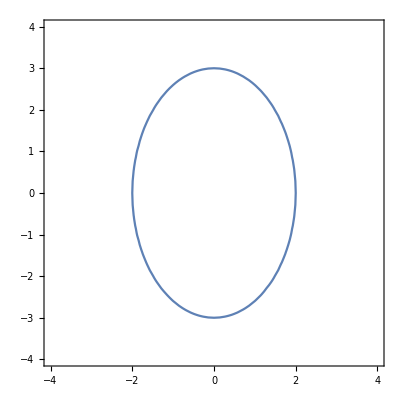

```mathematica
ContourPlot[9x^2+4y^2==36,{x,-4,4},{y,-4,4},Axes->True]
```

It drew an ellipse for us - the graph of the equation 9 x^2+4 y^2=36. You should look up ContourPlot in the documentation center. Here are some additional comments worth noting:
	1. Again, note the use of the double equal signs == to define a relation. Using one equal sign doesn’t work here.
	2.  I specifically described the ranges for x and y. Notice how that is done.
	3. There are ornamentations to the graphics that I can add. I chose to add the x and y axes. Try putting in False and compare.

## Play around with it: use ContourPlot to draw a parabola, a hyperbola, a line, a cubic, some with and some without axes.

We will want to look at several graphs at once. To do this, we will use the Show command. It combines a bunch of graphics into one picture. As an example, here are plots of the two equations we solved above:

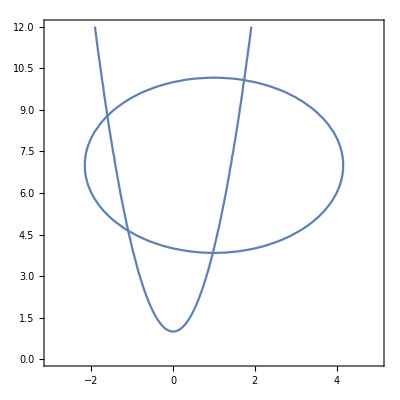

```mathematica
Show[ContourPlot[(x-1)^2+(y-7)^2==10,{x,-3,5},{y,0,12},Axes->True],ContourPlot[y==3 x^2+1,{x,-3,5},{y,0,12},Axes->True]]
```

## Here, the circle doesn’t look so circular. Read the ContourPlot commands carefully and see if you can see what’s going on. Can you change the bounds on the variables so that the picture contains a true circle. Briefly sum up what you think is happening.

## Get Mathematica to draw a picture of a parabola and a line tangent to the parabola at some point other that the vertex. If you want to show off, include a (visible) point of tangency in your picture. (You may need to look up the command “Point” in the documentation under the Help tab.)

Next, check this out.

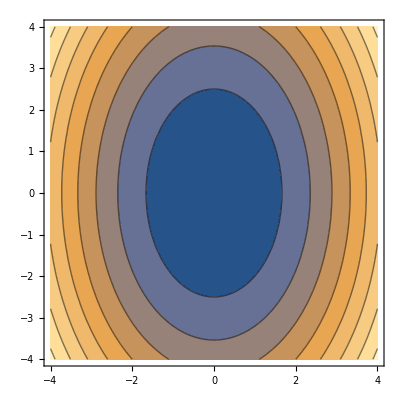

```mathematica
ContourPlot[9x^2+4y^2,{x,-4,4},{y,-4,4},Axes->True]
```

Did you see what was different about what we fed into ContourPlot? Here are the two commands right next to each other (evaluate them):

```mathematica
ContourPlot[9x^2+4y^2==36,{x,-4,4},{y,-4,4},Axes->True]
```

```mathematica
ContourPlot[9x^2+4y^2,{x,-4,4},{y,-4,4},Axes->True]
```

The difference is that in the second case, we didn’t set the expression 9x^2+4y^2 equal to anything. So, Mathematica chose a bunch of constants and plotted them together - with some pretty colors. If you haven’t yet, move the cursor across the picture to see which constants Mathematica chose. We will be using both of these versions of ContourPlot in the next technology assignment.

## Programming tools: Modules

Next, we will write our first program. In Mathematica, a program is called a “module”. The following bit of code defines a new command called “levelset”. It takes as input an expression in x and y (called e) and a value (called k). It returns a picture of the level set of f(x,y)=e at the value k.

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
```

Here are some notes on this Module: 
	1. When I define the module using the input variables e and k, I follow them with _’s. However, in the program, they are referred to as e and k without the _’s.
	2. Notice the colon-equal sign combo to define the module.
	3. The new variables k1 and set1 that I am going to use are put in braces at the start of the Module.
	4. The heart of this code is the Mathematica command ContourPlot.In fact, we see that the ContourPlot is a thing and I have defined set1 to be that thing (using a single =).
	5. Where is the picture? When we evaluate (control-return) that bit of code, it looks like nothing happened. But something did happen. Mathematica now knows what to do when I tell it to evaluate my program for specific inputs.

Here’s how it works to produce the level set of f(x,y)=3xy+2y corresponding to k=12 .

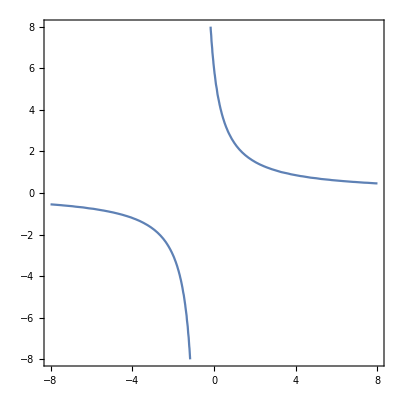

```mathematica
levelset[3 x y+2y,12]
```

Notes: 1. I had to leave a space between the x and the y in the expression 3xy+2y. That’s because Mathematica considers xy without a space to be one variable called xy.
	2. It’s convenient (or lucky) that the level set comes into the box where x and y are both between -8 and 8. What if k were 112? or 1112? Can you adjust the code of the level set module to get a better picture of these other level sets? 
	3. If I wanted to, I could adjust my code of the levelset module  so that the ranges for x and y were also inputs.

In the second technology assignment, we will use this to discuss LaGrange’s method for maximization.  Here, we will practice using this module to get the hang of it and to get the basics of modules.

## Play a little. Is it the case that every level set for f(x,y)=3xy+2y is a hyperbola? Explain.

## Also, change the input expression so that the corresponding level set is a parabola. 

##How about two lines intersecting lines? Two parallel lines? The goal here is to only use one levelset command.

## Next change the module itself. Write a module called levelsetwithbounds that takes as input an expression e, a value k and a number M and has as output the level set of f(x,y)=e corresponding to the level k between the ranges -M≤ x,y≤ M. Use your module to draw a picture of part of parabola containing the vertex where the vertex is more than 40 away from the origin.

## Programming tools: The “If” command

Here’s an example of a module with an “If” command. Evaluate it. You will see that I’ve annotated it (that is, put comments in the middle of my code). Mathematica ignores things in between (* and *).

```mathematica
log[n_]:=Module[{index},
If[n≤ 0,Return["Please enter a positive number"],Return[Log10[n]]]
(*This is the If command. It looks like this: 
If[_____,______,______] where the first entry is a condition and the second and third entries are actions. *)
(* It works like this:
If the condition in the first entry holds, it does the thing in the second entry. If the condition doesn't hold, it does the thing in the third entry.*)
]
```

## Try it out. Evaluate the module. Then enter and evaluate the following: 
log[100]
log[100000]
log[13.4]
log[-6]
Explain your results.

One last comment on the “If” command: we can use the If command with only two entries the first of which is a condition and the second is an action. In this case, if the condition holds, it does the action; if not, it does nothing. 

## Plug some numbers in to the following module (after evaluating it, of course).

```mathematica
ilikeevennumbers[n_]:=Module[{a},a=RandomInteger[2];
If[EvenQ[n],Return[{"Yippee!","Wonderful","Fantastic"}[[a+1]]]]
]
```

Explain what the module does.

## Programming Tools: Loops

Here is a Module with a loop. We will use the “While” command to make our loop. We could also us the “For” command. A bit of it is copied from a module I’ve already written. Evaluate the module.

```mathematica
sumofsquares[n_]:=Module[{index,sum},index=1;sum=0;
If[Or[n≤ 0,IntegerQ[n]==False],Return["Please enter a positive integer"]];
While[index≤n,sum=sum+index^2;index=index+1];
Return[sum]]
```

Plug in some numbers, some positive, some negative. Do you see what it’s doing?

```mathematica
sumofsquares[41]
```

If you’re unfamiliar with the concept of a loop, it can be a tough concept to get a handle on. Let’s go through this module slowly. Let’s start with the While command which is written:

		While[index≤n,sum=sum+index^2;index=index+1].

In general, it looks like this: While[---------, -----------;---------;--------------------; .... ]. The punctuation: a comma at the beginning, then things separated by semicolons. The first thing is a condition that might be true or false, the others are steps to take.

Our condition is about the quantity called “index”. Our first condition asks whether index is ≤ the number that was entered.

If it is, our module adds the square of the index to the quantity called “sum”. Then, it increases the index by 1.

After this, it reruns the While command with the new increased index. 

Lets plug in the number 3. Evaluate the following.

```mathematica
sumofsquares[3]
```

We did and we got the number 14. At one level, this is because 1^2 + 2^2 + 3^2 = 14. But let’s see how our module figured that out.

Here’s a schematic for what the module did. The Module is written in orange; the thoughts and actions of the computer are in purple.

sumofsquares[n_]:=Module[{index,sum},index=1;sum=0;

	The human gave me the number n=3.
	I’ll set index=1 and sum=0

If[Or[n≤ 0,IntegerQ[n]==False],Return[“Please enter a positive integer”]];

	I will check to see if either IntegerQ[3] is False or whether 3≤ 0. Since neither of these hold, I’ll move onto the next step

While[index≤n,sum=sum+index^2;index=index+1];

		Since the index =1 ≤  3, I’ll perform the following steps:
			sum=sum+index^2.  So, sum =0+1^2. So sum=1.
			Next, index=index+1. So index = 1+1. So index =2.

	Now I’ll redo the While command:

		Since the index =2 ≤  3, I’ll perform the following steps:
			sum=sum+index^2.  So, sum =1+2^2. So sum=5
			index=index+1. So index = 2+1. So index =3.

	Now I’ll redo the While command:

		Since the index =3 ≤  3, I’ll perform the following steps:
			sum=sum+index^2.  So, sum =5+3^2. So sum=14
			index=index+1. So index = 3+1. So index =4.

	Now I’ll redo the While command:

		Since the index=4 > 3, I won’t perform the following steps.

Return[sum]] 

	I’ll tell the human what the sum is at this point. “Hey human, sum=14”.

## Your turn. Write a module that takes as input a positive integer m prints the first m odd numbers and returns the square root of the sum of the numbers it printed. You should use the Print command in the module. Look it up in the Wolfram Documentation center available under the Help tab.

## Your assignment Problems

General instructions:

A. Copy the Your Assignment section into a new Mathematica notebook.
B. Copy the levelset module into the new notebook. Here it is for your convenience:

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
```

C. Place the answer to a question right after it. 
D. Remember to use alt + 7 to format cells in which you will be typing text. You don' t need to format cells in which you will be writing Mathematica code.

To submit
E. Save the notebook as yourname_assignment 1.nb
F. Evaluate entire notebook.
G. Save as a .pdf file.
H. Submit to Canvas These are due on Friday, March 11.

## In new cells, experiment by typing and evaluating the following:

        A. Solve[2x=7]
        B. a=9; Solve[2x==a] (that’s a semicolon in there)
        C. a=9 [Return] Solve[2x==a] (the carriage return is not Shift+Return).
        
Sum up what you have deduced about semi-colons, the Solve command, and use of equal signs. In particular, what’s the difference between B and C?

## In new cells, experiment with this by typing and evaluating the following:

      C. Solve [3x==y]
      D. Solve[3x==y,{x}].

Sum up what you have deduced about the Solve command and solving for particular variables.

## What are the pros and cons of using NSolve instead of Solve?

## Play around with the ContourPlot command: use ContourPlot to draw a parabola, a hyperbola, a line, and a cubic, some with and some without axes.

## Change the bounds on

Show[ContourPlot[(x-1)^2+(y-7)^2==10,{x,-3,5},{y,0,12},Axes→True],ContourPlot[y==3 x^2+1,{x,-3,5},{y,0,12},Axes→True]]

so that the circle comes out looking circular. (You’ll need to cut-and-paste it into a cell that isn’t formatted for text.) Briefly sum up what you think is happening.

## Get Mathematica to draw a picture of a parabola and a line tangent to the parabola at some point other than the vertex. If you want to show off, include a (visible) point of tangency in your picture. (You may need to look up the command “Point” in the documentation under the Help tab.)

## Play a little. Is it the case that every level set for f(x,y)=3xy+2y is a hyperbola? Explain.

## Change the input expression so that the corresponding level set is a parabola. 

## How about two lines intersecting lines? Two parallel lines? The goal here is to only use one levelset command.

## Next change the module itself. Write a module called levelsetwithbounds that takes as input an expression e, a value k and a number M and has as output the level set of f(x,y)=e corresponding to the level k between the ranges -M≤ x,y≤ M. (Our levelset module only draws the picture where M=8.) Use your module to draw a picture of part of parabola containing the vertex where the vertex is more than 40 away from the origin.

For the next question, you need the following module. Be sure to evaluate it.

```mathematica
log[n_]:=Module[{index},
If[n≤ 0,Return["Please enter a positive number"],Return[Log10[n]]]
(*This is the If command. It looks like this: 
If[_____,______,______] where the first entry is a condition and the second and third entries are actions. *)
(* It works like this:
If the condition in the first entry holds, it does the thing in the second entry. If the condition doesn't hold, it does the thing in the third entry.*)
]
```

## Evaluate the module. Then enter and evaluate the following: 
log[100]
log[100000]
log[13.4]
log[-6]
Explain your results.

## Plug a bunch of different kinds of numbers into the module below (after evaluating it).

```mathematica
ilikeevennumbers[n_]:=Module[{a},a=RandomInteger[2];
If[EvenQ[n],Return[{"Yippee!","Wonderful","Fantastic"}[[a+1]]]]
]
```

Explain what the module does.

##  Write a module that takes as input a positive integer m prints the first m positive odd numbers and returns the square root of the sum of the numbers it printed. You should use the Print command in the module. Look it up in the Wolfram Documentation center available under the Help tab.  Run your module for 3 different numbers between 20 and 50. Do you have any thoughts about the output?